```mathematica
f1[x_] := x
```

```mathematica
f2[x_] := 3 - x
```

```mathematica
f3[x_] := Sin[x]
```

```mathematica
alpha = -0.4
```

```mathematica
-0.4
```

```mathematica
g[x_] = ( f1[x]*Exp[alpha*f1[x]] + f2[x]*Exp[alpha*f2[x]] + f3[x]*Exp[alpha*f3[x]] )/( Exp[alpha*f1[x]] + Exp[alpha*f2[x]] + Exp[alpha*f3[x]] )
```

(ⅇ^(-0.4 (3-x)) (3-x)+ⅇ^(-0.4 x) x+ⅇ^(-0.4 Sin[x]) Sin[x])/(ⅇ^(-0.4 (3-x))+ⅇ^(-0.4 x)+ⅇ^(-0.4 Sin[x]))

```mathematica
(ⅇ^(2 x) x+ⅇ^(2 x^2) x^2+ⅇ^(2 Sin[x]) Sin[x])/(ⅇ^(2 h1[x])+ⅇ^(2 h2[x])+ⅇ^(2 h3[x]))
g[1]
```

(ⅇ^(2 x) x+ⅇ^(2 x^2) x^2+ⅇ^(2 Sin[x]) Sin[x])/(ⅇ^(2 h1[x])+ⅇ^(2 h2[x])+ⅇ^(2 h3[x]))

1.18328

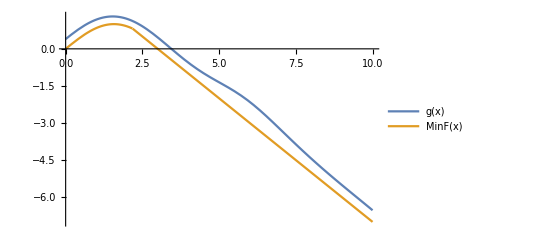

```mathematica
Plot[{g[x],MinF[x]},{x,0,10},PlotLegends->"Expressions"]
```

```mathematica
MinF[x_] = Min[f1[x],f2[x],f3[x]]
```

Min[3-x,x,Sin[x]]

```mathematica
Plot[Min[f1[x],f2[x],f3[x]],{x,0,10}]
```

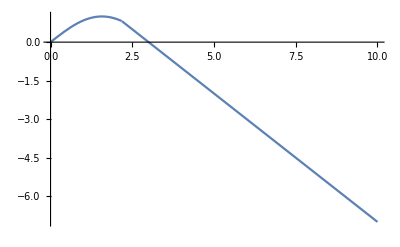

```mathematica
m[x_] = Grad[g[x],{x}]
```

{-(((0.4 ⅇ^(-0.4 (3-x))-0.4 ⅇ^(-0.4 x)-0.4 ⅇ^(-0.4 Sin[x]) Cos[x]) (ⅇ^(-0.4 (3-x)) (3-x)+ⅇ^(-0.4 x) x+ⅇ^(-0.4 Sin[x]) Sin[x]))/(ⅇ^(-0.4 (3-x))+ⅇ^(-0.4 x)+ⅇ^(-0.4 Sin[x]))^2)+(-ⅇ^(-0.4 (3-x))+ⅇ^(-0.4 x)+0.4 ⅇ^(-0.4 (3-x)) (3-x)-0.4 ⅇ^(-0.4 x) x+ⅇ^(-0.4 Sin[x]) Cos[x]-0.4 ⅇ^(-0.4 Sin[x]) Cos[x] Sin[x])/(ⅇ^(-0.4 (3-x))+ⅇ^(-0.4 x)+ⅇ^(-0.4 Sin[x]))}

```mathematica
m[1]
```

{0.466542}

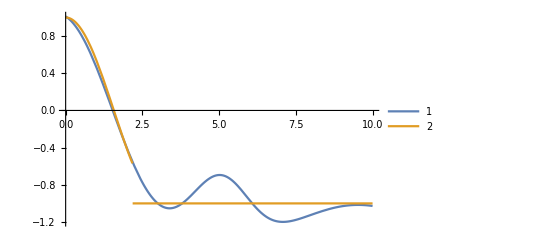

```mathematica
Plot[{m[x],MinFgrad[x]},{x,0,10},PlotLegends->Automatic]
```

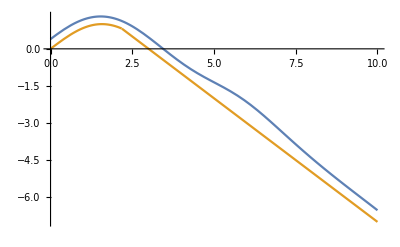

```mathematica
m[1]
```

{0.466542}

```mathematica
MinFgrad[x_] = Grad[MinF[x],{x}]
```

{Piecewise[{{-1, x≥3/2&&x+Sin[x]≥3}, {1, x<3/2&&x-Sin[x]≤0}, {Cos[x], True}}]}

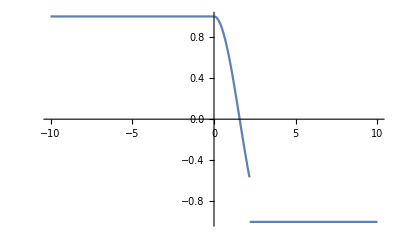

```mathematica
Plot[MinFgrad[x],{x,-10,10}]
```

```mathematica
g2[f1_,f2_,f3_,x_] = ( f1[x]*Exp[alpha*f1[x]] + f2[x]*Exp[alpha*f2[x]] + f3[x]*Exp[alpha*f3[x]] )/( Exp[alpha*f1[x]] + Exp[alpha*f2[x]] + Exp[alpha*f3[x]] )
```

(ⅇ^(-0.4 (3-x)) (3-x)+ⅇ^(-0.4 x) x+ⅇ^(-0.4 Sin[x]) Sin[x])/(ⅇ^(-0.4 (3-x))+ⅇ^(-0.4 x)+ⅇ^(-0.4 Sin[x]))

```mathematica
gF1[x_] = Grad[g2[f1,f2,f3,x],{f1,f2,f3}]
```

Set::write: Tag List in {g2'[f1]}[x_] is Protected.

```mathematica
rat[x1_,x2_,alpha_,l_,sigma_] = sigma^2 * ( 1 + 1/2/alpha/l/l* Norm[x1-x2] )^(-alpha)
```

sigma^2 (1+Norm[x1-x2]/(2 alpha l^2))^-alpha

```mathematica
Grad[rat[x1,x2,alpha,l,sigma],{sigma}]
```

{2 sigma (1+Norm[x1-x2]/(2 alpha l^2))^-alpha}

```mathematica
Grad[rat[x1,x2,alpha,l,sigma],{l}]
```

{(sigma^2 Norm[x1-x2] (1+Norm[x1-x2]/(2 alpha l^2))^(-1-alpha))/l^3}

```mathematica
gamma[x_] = Integrate[z^(x-1)Exp[-z],{z,0,Infinity}]
```

ConditionalExpression[Gamma[x], Re[x]>0]

```mathematica
gamma[20]
```

121645100408832000

```mathematica
Gamma[20]
```

121645100408832000

```mathematica
g = ChiSquareDistribution[2]
```

ChiSquareDistribution[2]

```mathematica
Evaluate[ChiSquareDistribution[2][2]]
```

ChiSquareDistribution[2][2]

```mathematica
PDF[ChiSquareDistribution[7],5]
```

(5 √(5/(2 π)))/(3 ⅇ^(5/2))

```mathematica
1/(2 ⅇ)
```

1/(2 ⅇ)

```mathematica
ff[ x_] = PDF[ChiSquareDistribution[7],x]
```

Piecewise[{{(ⅇ^(-x/2) x^(5/2))/(15 √(2 π)), x>0}, {0, True}}]

```mathematica
ff[5]
```

(5 √(5/(2 π)))/(3 ⅇ^(5/2))

```mathematica
Q[x_,y_] = 5*x^2 - 2*x*y + 2*y^2
```

5 x^2-2 x y+2 y^2

```mathematica
Reduce[Q[x,y]>=0,{x,y}]
```

```mathematica
(x|y)∈Reals
```

(x|y)∈ℝ

```mathematica
h = 7
```

7

```mathematica
A = {{a b}, {c d}}
```

{{a b},{c d}}

```mathematica
Inverse[A] //MatrixForm
```

Inverse::matsq: Argument {{a b},{c d}} at position 1 is not a non-empty square matrix.

```mathematica
Inverse[{{a b},{c d}}]
```

Inverse::matsq: Argument {{a b},{c d}} at position 1 is not a non-empty square matrix.

Inverse[{{a b},{c d}}]

```mathematica
Inverse[{{a,b},{c,d}}]
```

{{d/(-b c+a d),-b/(-b c+a d)},{-c/(-b c+a d),a/(-b c+a d)}}

```mathematica
Inverse[{{x11,x12,x13},{x21,x22, x23}, {x31, x32, x33}}] //Simplify[x12=x21, x13=x31, x23=x32]
```

Simplify::nonopt: Options expected (instead of x32) beyond position 2 in Simplify[x21,x31,x32]. An option must be a rule or a list of rules.

```mathematica
Simplify[x21,x31,x32][{{(-x32^2+x22 x33)/(-x22 x31^2+2 x21 x31 x32-x11 x32^2-x21^2 x33+x11 x22 x33),(x31 x32-x21 x33)/(-x22 x31^2+2 x21 x31 x32-x11 x32^2-x21^2 x33+x11 x22 x33),(-x22 x31+x21 x32)/(-x22 x31^2+2 x21 x31 x32-x11 x32^2-x21^2 x33+x11 x22 x33)},{(x31 x32-x21 x33)/(-x22 x31^2+2 x21 x31 x32-x11 x32^2-x21^2 x33+x11 x22 x33),(-x31^2+x11 x33)/(-x22 x31^2+2 x21 x31 x32-x11 x32^2-x21^2 x33+x11 x22 x33),(x21 x31-x11 x32)/(-x22 x31^2+2 x21 x31 x32-x11 x32^2-x21^2 x33+x11 x22 x33)},{(-x22 x31+x21 x32)/(-x22 x31^2+2 x21 x31 x32-x11 x32^2-x21^2 x33+x11 x22 x33),(x21 x31-x11 x32)/(-x22 x31^2+2 x21 x31 x32-x11 x32^2-x21^2 x33+x11 x22 x33),(-x21^2+x11 x22)/(-x22 x31^2+2 x21 x31 x32-x11 x32^2-x21^2 x33+x11 x22 x33)}}]
```

```mathematica
test[x_] = x^2
```

x^2